```mathematica
H[k_]:=ArrayFlatten[Table[(n*W*PauliMatrix[0]+Q*PauliMatrix[3])*If[n==m,1,0]+I^(m-n)*BesselJ[m-n,F]*Cos[k-(m-n)*Pi/2]*PauliMatrix[1],{n,-Nm,Nm},{m,-Nm,Nm}]];
a0[k_]:=-1/Sqrt[2]*Sqrt[1-Q/Sqrt[Q^2+Cos[k]^2]];
b0[k_]:=1/Sqrt[2]*Sqrt[1+Q/Sqrt[Q^2+Cos[k]^2]];
E0[k_]:=-Sqrt[Q^2+Cos[k]^2];
A[k_]:=SortBy[Transpose[Eigensystem[H[k]]],First][[2*Nm+1,2]];
Xa[k_]:={Sum[A[k][[2i-1]],{i,1,2*Nm+1}],Sum[A[k][[2i]],{i,1,2*Nm+1}]};
wa[k_]:=Conjugate[Xa[k]].{a0[k],b0[k]};
B[k_]:=SortBy[Transpose[Eigensystem[H[k]]],First][[2*Nm+2,2]];
Xb[k_]:={Sum[B[k][[2i-1]],{i,1,2*Nm+1}],Sum[B[k][[2i]],{i,1,2*Nm+1}]};
wb[k_]:=Conjugate[Xb[k]].{a0[k],b0[k]};
Bound[l_]=If[-Nm-1<l<Nm+1,1,0];
ChiA[k_,j_]:=If[-Nm-1<j<Nm+1,{A[k][[2(j+Nm)+1]],A[k][[2(j+Nm)+2]]},{0,0}];
ChiB[k_,j_]:=If[-Nm-1<j<Nm+1,{B[k][[2(j+Nm)+1]],B[k][[2(j+Nm)+2]]},{0,0}];
IHknl[k_,N0_,n_,l_]:=(Abs[wa[k]]^2*Conjugate[ChiA[k,(n-l+N0)]].PauliMatrix[1].ChiA[k,n]+Abs[wb[k]]^2*Conjugate[ChiB[k,(n-l+N0)]].PauliMatrix[1].ChiB[k,n])*I^l*BesselJ[l,F]*Sin[k+l*Pi/2];
IHk[N0_,k_]:=ParallelSum[IHknl[k,N0,n,l],{n,-Nm,Nm},{l,-Nm,Nm}];
IH[N0_]:=Sum[IHk[N0,-Pi/2+Pi/Nk*i],{i,0,Nk}];
```

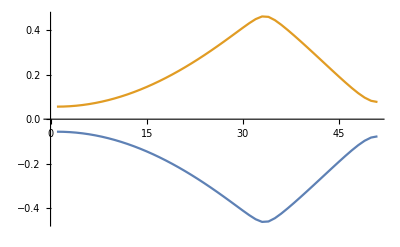

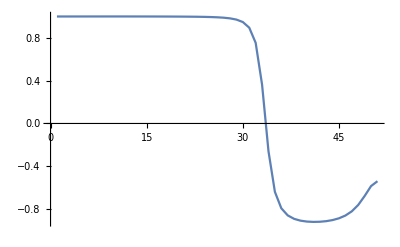

```mathematica
Nm=3;
W=1;
F=0.5;
Q=0.1;
NN=50;
ListLinePlot[{Table[Sort[Eigenvalues[H[i*Pi/(2*NN)]]][[2*Nm+1]],{i,0,NN}],Table[Sort[Eigenvalues[H[i*Pi/(2*NN)]]][[2*Nm+2]],{i,0,NN}]}]
ListLinePlot[Table[Abs[wb[i*Pi/(2*NN)]]^2-Abs[wa[i*Pi/(2*NN)]]^2,{i,0,NN}]]
```

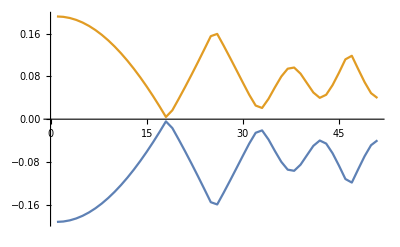

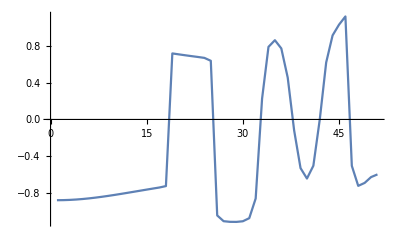

```mathematica
Nm=3;
W=0.25;
F=0.5;
Q=0.1;
NN=50;
ListLinePlot[{Table[Sort[Eigenvalues[H[i*Pi/(2*NN)]]][[2*Nm+1]],{i,0,NN}],Table[Sort[Eigenvalues[H[i*Pi/(2*NN)]]][[2*Nm+2]],{i,0,NN}]}]
ListLinePlot[Table[Abs[wb[i*Pi/(2*NN)]]^2-Abs[wa[i*Pi/(2*NN)]]^2,{i,0,NN}]]
```

```mathematica
W=0.1;
F=0.1;
Q=0.01;
```

```mathematica
Nm=3;
Nk=3;
IH[1]
IH[3]
```

$Aborted

```mathematica
Nm=10;
Nk=10;
IH[1]
IH[3]
```

0.+8.47378×10^-7 ⅈ

$Aborted

```mathematica
Nm=10;
Nk=10;
IH[1]
IH[3]
IH[5]
```

0.-0.00830317 ⅈ

0.+0.0122394 ⅈ

```mathematica
Nm=10;
Nk=20;
IH[1]
IH[3]
IH[5]
```

4.23534×10^-34+0.000759191 ⅈ

0.-0.0082492 ⅈ

-7.74462×10^-33+0.0134553 ⅈ

```mathematica
Nm=10;
Nk=30;
IH[1]
IH[3]
IH[5]
```

-9.68078×10^-34+0.00106267 ⅈ

0.-0.0111238 ⅈ

-1.03262×10^-32+0.0143081 ⅈ

```mathematica
Nm=10;
Nk=50;
IH[1]
```

0.+1.461×10^-16 ⅈ

-2.46519×10^-32+1.89182×10^-8 ⅈ

```mathematica
Nm=10;
Nk=100;
IH[1]
```

2.46519×10^-32+3.64067×10^-8 ⅈ

```mathematica
Nm=10;
Nk=200;
IH[1]
```

0.+7.14686×10^-8 ⅈ

```mathematica
Nk=300;
IH[1]
```

$Aborted